{-337872.,-7.02164×10^7,2.91509×10^8,7.00131×10^8,6.67671×10^8,7.08361×10^8,1.07045×10^9,1.36777×10^9}

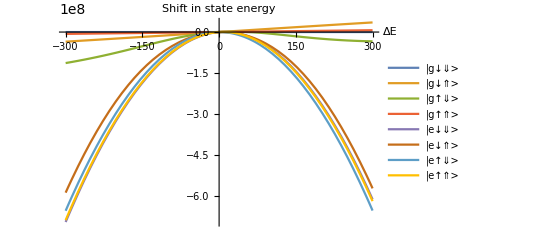

```mathematica
setVariables[]

{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {0, 0.20112299109490023, 222.4901014437078,0.014875274142248585,3.486194421243477*^10,3.472501636059094*^10,1.1474933117467306*^-7};

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/10, Tmax]^2;
ωE = ωEin;
ωB = ωBin;
Tmax = Tmaxin;

t = 0;

EsAt0 = energiesInOrder[Hcorrected]

Clear[ΔE]
Plot[{
EsAt0[[1]] - energiesInOrder[Hcorrected][[1]],
EsAt0[[2]] - energiesInOrder[Hcorrected][[2]],
EsAt0[[3]] - energiesInOrder[Hcorrected][[3]],
EsAt0[[4]] - energiesInOrder[Hcorrected][[4]],
EsAt0[[5]] - energiesInOrder[Hcorrected][[5]],
EsAt0[[6]] - energiesInOrder[Hcorrected][[6]],
EsAt0[[7]] - energiesInOrder[Hcorrected][[7]],
EsAt0[[8]] - energiesInOrder[Hcorrected][[8]]
}, {ΔE, -300, 300}, PlotLegends->basisGE, AxesLabel->{"ΔE", "Shift in state energy"}]



clearVariables[]
```